## Contour plots from data saved in .txt files

```mathematica
ClearAll["Global`*"]
```

### Directory

```mathematica
SetDirectory[NotebookDirectory[]];
folder = "";
filename = "intlog-param-1-dS-PRD-v2";
```

### Read text file

```mathematica
dataTable = Import[FileNameJoin[{Directory[],folder,StringJoin[filename,".txt"]}],"Table"];
time = Import[FileNameJoin[{Directory[],folder,StringJoin[filename,"-time",".txt"]}],"Table"];
parameter = Import[FileNameJoin[{Directory[],folder,StringJoin[filename,"-parameter",".txt"]}],"Table"];
```

### Table plot

```mathematica
maxT = Max[time];
minp = Min[parameter];
maxp=Max[parameter];
```

```mathematica
<<MaTeX`
```

#### When varying other parameters

```mathematica
dataTableExt=dataTable[[1;;;;2,1;;;;1]];
```

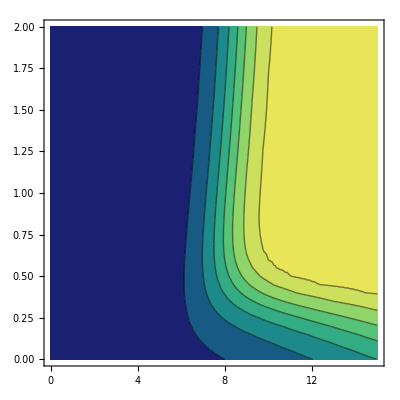

```mathematica
pstring="d_S";
plot=ListContourPlot[ToExpression[dataTableExt],PlotRange->All,Contours->Append[Table[k,{k,0,0.90,0.15}],0.99],ColorFunctionScaling->False,ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{double}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX[pstring,Magnification->2.5]},PlotRange->All,DataRange->{{0,maxT},{minp,maxp}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

#### When varying Δt_B

```mathematica
Dimensions[dataTable]
```

{11,111}

```mathematica
dataTable=dataTable[[All, 1;;141]];
```

```mathematica
pstring="\\Delta t_B";
plot=ListContourPlot[ToExpression[dataTable],PlotRange->All,Contours->Append[Table[k,{k,0,0.90,0.05}],0.99],ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False, PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"LM Roman 12"},LegendLabel->MaTeX["P_{R}^{\\text{double}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX[pstring,Magnification->2.5]},PlotRange->All,DataRange->{{0,maxT},{minp,maxp}}, BaseStyle->{FontColor->"Black",FontFamily -> "LM Roman 12",FontSize->22},Frame->True]
```

-Graphics-

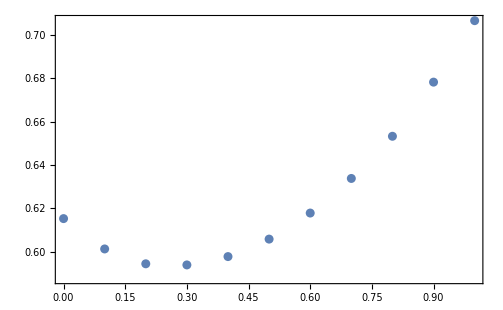

```mathematica
plotcut=ListPlot[dataTable[[All, 111]],FrameLabel->{MaTeX["\\Delta t_B",Magnification->2.5],MaTeX["P_{R}^{\\text{double}}",Magnification->2.5]},PlotRange->All,DataRange->{minp,maxp},BaseStyle->{FontColor->"Black",FontFamily -> "LM Roman 12",FontSize->22},Frame->True]
```

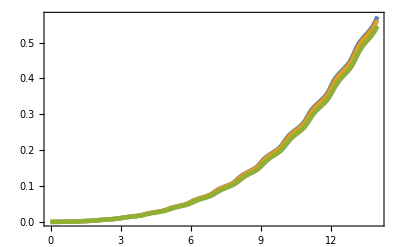

```mathematica
plote=ListPlot[{dataTable[[1]],dataTable[[2]],dataTable[[3]]},BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["T", Magnification->1.5],MaTeX["P_R^{\\text{double}}",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["\\Delta t_B = 0", Magnification->1.2],MaTeX["\\Delta t_B = 0.5", Magnification->1.2],MaTeX["\\Delta t_B = 1", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.19,0.71}],Joined->True, DataRange->{0,14},PlotStyle->{Thickness[0.008]}]
```

#### When varying μ_A

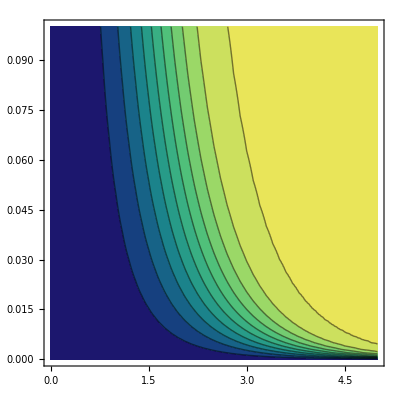

```mathematica
plot=ListContourPlot[dataTable,PlotRange->All,Contours->Append[Table[k,{k,0,0.99,0.1}],0.99],ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{double}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX["\\mu_A",Magnification->2.5]},PlotRange->All,DataRange->{{0,maxT},{minp,maxp}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

#### When varying n_0

```mathematica
dataTableExt=dataTable[[11;;;;1,1;;;;5]];
```

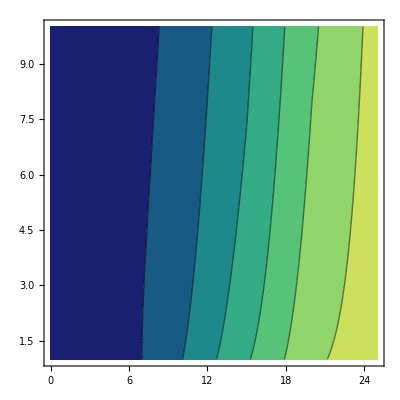

```mathematica
plot=ListContourPlot[ToExpression[dataTableExt],PlotRange->All,Contours->Append[Table[k,{k,0,0.99,0.15}],0.99],ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{double}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX["n_0 (\\times 10^5)",Magnification->2.5]},PlotRange->All,DataRange->{{0,maxT},{1,10}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

#### When varying k_i

```mathematica
Dimensions[dataTable]
```

{100,101}

```mathematica
Dimensions[dataTableExt]
```

{50,101}

```mathematica
dataTableExt=dataTable[[1;;;;1,1;;;;2]];
```

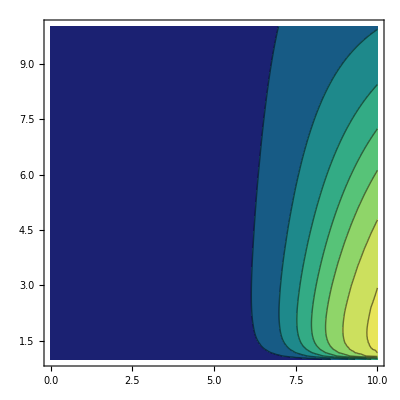

```mathematica
plot=ListContourPlot[ToExpression[dataTableExt],PlotRange->All,ColorFunctionScaling -> False,Contours->Append[Table[k,{k,0,0.99,0.15}],0.99],ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{double}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX["k_S(\\times 10^{5})",Magnification->2.5]},PlotRange->All,DataRange->{{0,maxT},{1,10}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

#### When varying k_i (cut)

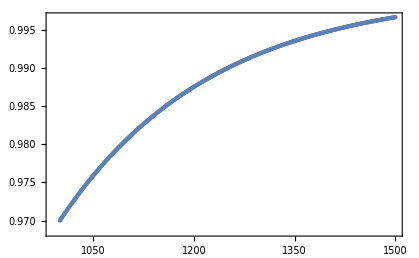

```mathematica
plotcut=ListPlot[dataTable[[All, 1]],FrameLabel->{MaTeX["k_S",Magnification->2.5],MaTeX["P_{R}^{\\text{single}}",Magnification->2.5]},PlotRange->All,DataRange->{1000,1500},BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True, ImageSize->Large]
```

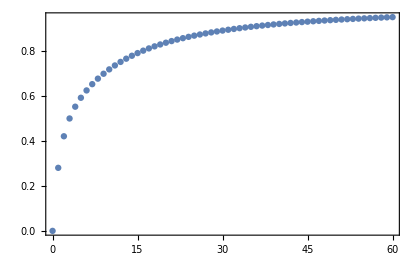

```mathematica
ListPlot[dataTable[[5, All]],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX["P_{R}^{\\text{single}}",Magnification->2.5]},PlotRange->All,DataRange->{0,60},BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True, ImageSize->Large]
```

### Export new pdf figure

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Export[FileNameJoin[{Directory[],StringJoin[filename,"","-v3.pdf"]}],plot]
(*Export[StringJoin[filename,"-PRD2D",".pdf"],plote]*)
```

```mathematica
Export[FileNameJoin[{Directory[],StringJoin[filename,"",".pdf"]}],plotcut]
```